# HW 3

Vector Norms

What is the default vector norm?

```mathematica
?Norm
```

The default vector norm is the 2 norm.

```mathematica
Norm[{x1,x2,x3}]
```

√(Abs[x1]^2+Abs[x2]^2+Abs[x3]^2)

Matrix Norms

What is the default matrix norm?

The default matrix norm is the induced 2 norm.

```mathematica
{m,n}={12,5};
A=RandomReal[{-1,1},{m,n}];
{Norm[A], Norm[A,2],SingularValueList[A,2]}
```

{2.38532,2.38532,{2.38532,2.05637}}

In either a Julia or Mathematica notebook use linear algebra to fit polynomials to
	atan(1+3 sin(x)+cos^2(3x)+ln(1+x^2))
using n equally spaced points on the interval [-1,1].

```mathematica
{a,b}={-1.0,1.0};
n=4;
f[x_]:= ArcTan[1 + 3 Sin[x]+Cos[3x]^2+Log[1+x^2]]
xs=Range[a,b,(b-a)/(n-1)];
fs=f[xs];
A=Table[xs^i,{i,0,n-1}]ᵀ;
MatrixForm[A]
as =LinearSolve[A,fs];
p4[x_]=Sum[as⟦i⟧x^(i-1),{i,n}]
```

(1. | -1. | 1. | -1.
1. | -0.333333 | 0.111111 | -0.037037
1. | 0.333333 | 0.111111 | 0.037037
1. | 1. | 1. | 1.)

0.785811+1.23731 x-0.0215812 x^2-0.620814 x^3

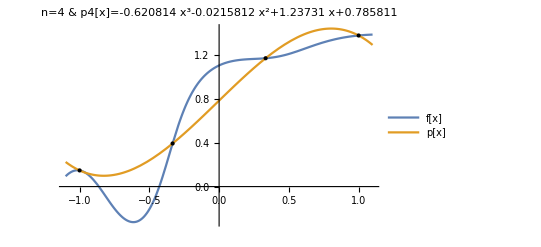

```mathematica
Plot[{f[x], p4[x]}, {x, a - ϵ, b + ϵ},
 PlotLabel -> StringForm["n=`` & p4[x]=``", n, p4[x]],
 PlotLegends -> {"f[x]", "p4[x]"},
 Epilog -> Point[{xs, fs}ᵀ]]
```

Display/show the matrix for n=4.

Plot the function and the fitted polynomials for n=4,10.  Make sure your functions are labelled and that your plot extends a little bit outside the sampled region.

1.12028+0.566384 x-3.51847 x^2+7.67939 x^3+4.15808 x^4-22.8866 x^5+2.37328 x^6+23.7065 x^7-3.36894 x^8-8.44917 x^9

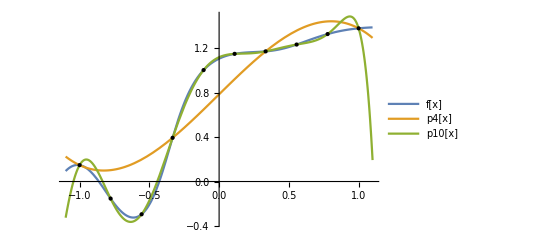

```mathematica
n=10;
xs=Range[a,b,(b-a)/(n-1)];
fs=f[xs];
A=Table[xs^i,{i,0,n-1}]ᵀ;
as =LinearSolve[A,fs];
p10[x_]=Sum[as⟦i⟧x^(i-1),{i,n}]
Plot[{f[x], p4[x],p10[x]}, {x, a - ϵ, b + ϵ},
 PlotLegends -> {"f[x]", "p4[x]","p10[x]"},
 Epilog -> Point[{xs, fs}ᵀ]]
```

Comment on the quality of the fit outside the region.

With more points the fit is better inside the region.  The 10 point version goes bad faster outside the region!